# Lindblad equations for a single atom interacting with classical fields and a single photon.

P. Huft

Adapted from my notebook “lindblad_single_atom_single_photon.nb”.

This notebook is for modeling single photon absorption by a multilevel atom, where two classical fields are used for a STIRAP process with the photon.

## definitions

```mathematica
(*the Schrodinger picture operators, or equivalently the Heisenberg ops at t=t0*)
σ0=PauliMatrix[0];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σp=1/2(σx+I σy);
σm=1/2(σx-I σy);
a=σm;
adag=σp;
dag[z_]=ConjugateTranspose[z];

(*operators in the atom-field space with the Fock state basis truncated at N=1*)
aa=KroneckerProduct[a,σ0];
sm=KroneckerProduct[σ0,σm];
sp=dag[sm];
sz=KroneckerProduct[σ0,σz];
II=KroneckerProduct[σ0,σ0];

BuildMasterEq[ρ0_,H_, Llist_:{},t0_:0]:=Module[{dim,rho,eqIdcs,comm,linblad,rhoPruned,eqsPruned,rhoICPruned, popIdxList, cohIdxList, i, j,m,L},
(*The code below builds the equations to be passed to NDSolve, removing the redundant equations (since Subscript[ρ, ij]=Subscript[ρ, ji]^*).

"Pruned" variables refer to the eqs which have had the redundant elements removed.

Args: 
 ρ0: the initial density matrix;
	H: the Hamiltonian;
	L: the jump operators. I assume that decay constants γ are accounted for in L, which is to say that the Linblad term looks like (L ρ L^†-1/2(ρ L^†L +L^†L ρ)) rather than γ(L ρ L^†-1/2(ρ L^†L +L^†L ρ));
	t0: the initial time, which is 0 if not specified.

Returns: eqsPruned, rhoICPruned (the pruned initial state), rhoPruned (the pruned set of variables, i.e. elements of ρ, to solve for), popIdxList (the indices of the population terms), cohIdxList (inds of the coherence terms)
*)
Clear[ρ,t];
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t]&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm =  H.rho-rho.H  ;
linblad=Array[0&,{dim,dim}];
For[m=1,m<Length[Llist]+1,m++,
L=Llist[[m]];
linblad +=L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);
];
(*linblad =L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);*)
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-I comm[[i,j]]+linblad[[i,j]]];
AppendTo[rhoICPruned,(rho/.t-> t0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]];
(*Print[eqsPruned[[-1]]]*)
];
];
];
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems+1,i++,
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
];
{eqsPruned,rhoICPruned,rhoPruned, popIdxList, cohIdxList}
];
```

## two-level atom + single photon

This section is adapted from my notebook “lindblad_single_atom_single_photon.nb”, and compares the results of “input-output theory” for dealing a quantum emitter interacting with quantum light with the results of “Efficient excitation of a single atom with single photons” by the Scarani group.

Reproduce Figs. 1 and 4 of the Scarani paper, by solving the Heisenberg-Langevin equations as well as the density matrix equation.

### Hamiltonian + Lindblad from input-output theory

See “Quantum interactions with pulses of radiation” by Kiilerich and Molmer. It’s not clear that I’m correctly applying their theory, since input-output theory and cascaded systems as they discuss are “uni-directional”. In Scarani, a fraction of the atomic decay goes back into the pulse mode, while in input-output theory, the outgoing pulse mode would have its own set of operators and I would have to reformulate the problem slightly. In any case, the results here are closer to the Scarani result.

#### account for input field mode only

This is very close! It only disagrees with Scarani for the bandwidth Ω>>Γ, which is unlikely to be true for the theory of interest. Todo: reproduce Pe plots for other choices of pulse shapes.

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Time to run sim step 1: 0.171875

Time to run sim step 2: 0.15625

Time to run sim step 3: 0.15625

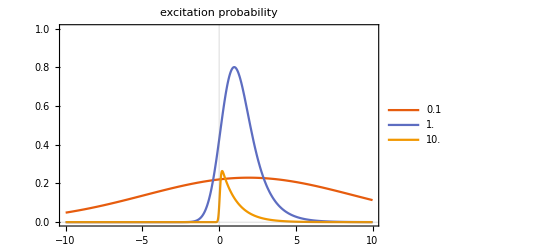

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

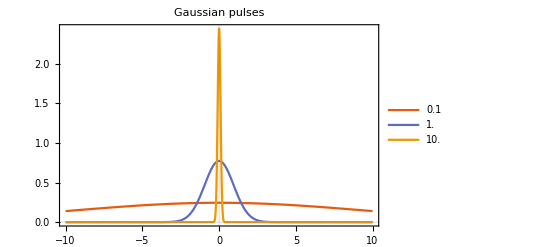

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

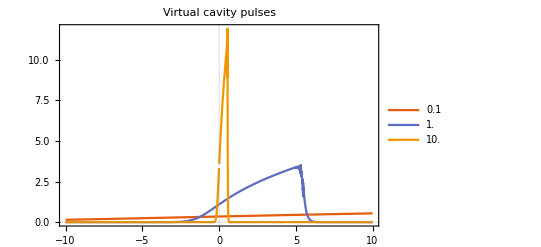

```mathematica
Γ=1;
Γp=Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;
t0=0;

Ωarr={0.1,1,10}Ω0;
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
VirtualCavityPulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

u=(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
(*gu=u/(√(1-(Ω^2/(2π))^(1/2)(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))));*)

(*it works better if the integral is done with a definite value for Ω*)
gu=u/(√(1-(Ω^2/(2π))^(1/2)Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,-∞,t}]));
AppendTo[PulseArr, u];
AppendTo[VirtualCavityPulseArr, gu];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
Plot[VirtualCavityPulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Virtual cavity pulses",PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
VirtualCavityPulseArr[[3]]
```

(2.44625 ⅇ^(-56.25 t^2))/(√(1-0.0333333 (15.+15. Erf[10.6066 t])))

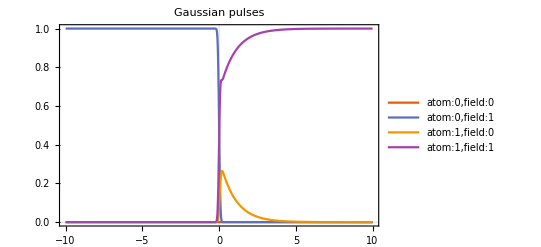

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

Trying to understand where the singularity arises for short pulses

```mathematica
Clear[Ω,t0]
(*Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,0,t}]*)
Integrate[Exp[-(Ω (t-t0))^2/4]^2,{t,-∞,t}]
```

ConditionalExpression[(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2)), Re[Ω^2]≥0]

```mathematica
(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))
```

```mathematica
(√(π/2) (Ω+√(Ω^2) 1))/(Ω √(Ω^2))
```

(√(π/2) (Ω+√(Ω^2)))/(Ω √(Ω^2))

```mathematica
Plot[(1-(Ω^2/(2π))^(1/2)(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))/.{t0->0,Ω->15}),{t,-10,10}]
```

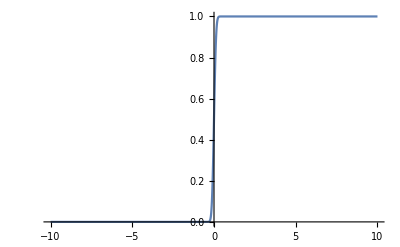

```mathematica
Plot[((Ω^2/(2π))^(1/2)(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2))/.{t0->0,Ω->10}),{t,-10,10}]
```

```mathematica
√(1-(Ω^2/(2π))^(1/2)(√(π/2) (Ω+√(Ω^2) Erf[((t-t0) Ω)/(√2)]))/(Ω √(Ω^2)))
```

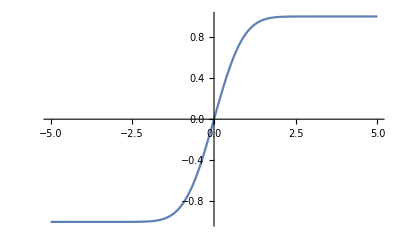

```mathematica
Plot[Erf[x],{x,-5,5}]
```

### compare input-output theory and H.-L. for various pulse shapes - correct

#### define pulse shapes and simulation parameters

```mathematica
Clear[Ω];
gaussian=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];sech=√(Ω/2)Sech[Ω t];
rect=Piecewise[{{√(Ω/2),0<=t<=2/Ω},{0,t>2/Ω}}];
symm=√Ω Exp[-Ω Abs[t]];
decay=Piecewise[{{√Ω Exp[-Ω t/2],t>0}}];
rising=Piecewise[{{√Ω Exp[Ω t/2],t<0}}];
PulseArr={gaussian,sech,rect,symm,decay,rising};
PulseLegend={"Gaussian", "Hyperbolic secant", "Rect", "Symm. exponential", "Decaying exponential", "Rising exponential"};
Γ=1;
Γp=Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;

Ω=Ω0;
```

#### Lindblad eq for various pulse shapes

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[H,L,t,ρ,rho]
PeLindbladArr={};

For[i=1,i<Length[PulseArr]+1,i++,
u=PulseArr[[i]];
uSquaredIntegral=Assuming[t∈Reals,Integrate[u^2/.t->τ,{τ,-∞,t}]];
gu=u/(√(1-uSquaredIntegral));

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeLindbladArr,Pe];
]
```

Time to run sim step 1: 0.0625

Time to run sim step 2: 0.0625

NDSolve::ndsz: At t == 1.33333, step size is effectively zero; singularity or stiff system suspected.

Time to run sim step 3: 0.203125

Time to run sim step 4: 0.078125

Time to run sim step 5: 0.078125

Time to run sim step 6: 0.0625

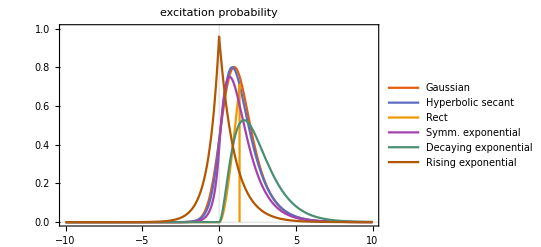

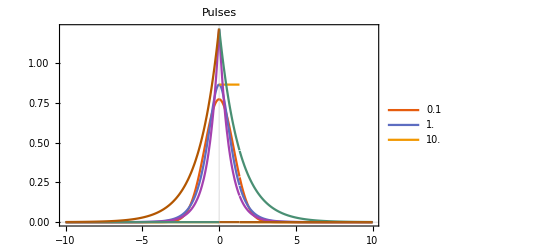

```mathematica
Plot[PeLindbladArr,{t,tmax-2tmax,tmax},PlotLegends->PulseLegend,PlotLabel->"excitation probability",PlotRange->{{tmax-2tmax,tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2tmax,tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Heisenberg-Langevin eqs for various pulse shapes

```mathematica
Clear[s,M,b,t]
PeHLArr={};
For[i=1,i<Length[PulseArr]+1,i++,
g=PulseArr[[i]];
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeHLArr,Pe];
]
```

Time to run sim step 1: 0.

Time to run sim step 2: 0.015625

Time to run sim step 3: 0.015625

Time to run sim step 4: 0.

Time to run sim step 5: 0.

Time to run sim step 6: 0.015625

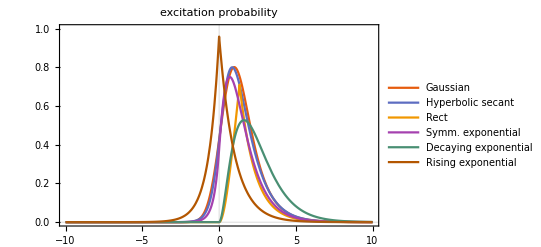

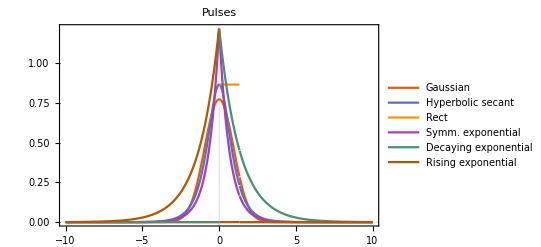

```mathematica
Plot[PeHLArr,{t,tmax-2(tmax),tmax},PlotLegends->PulseLegend,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax),tmax},PlotLegends->PulseLegend,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Compare the solutions from the two methods

The plot below shows that the input-output theory Lindblad equation and Heisenberg-Langevin equations agree for all pulse shapes, except where t>2/Ω for the rectangular pulse, which is because Mathematica didn’t properly integrate it in the calculation of g(t).

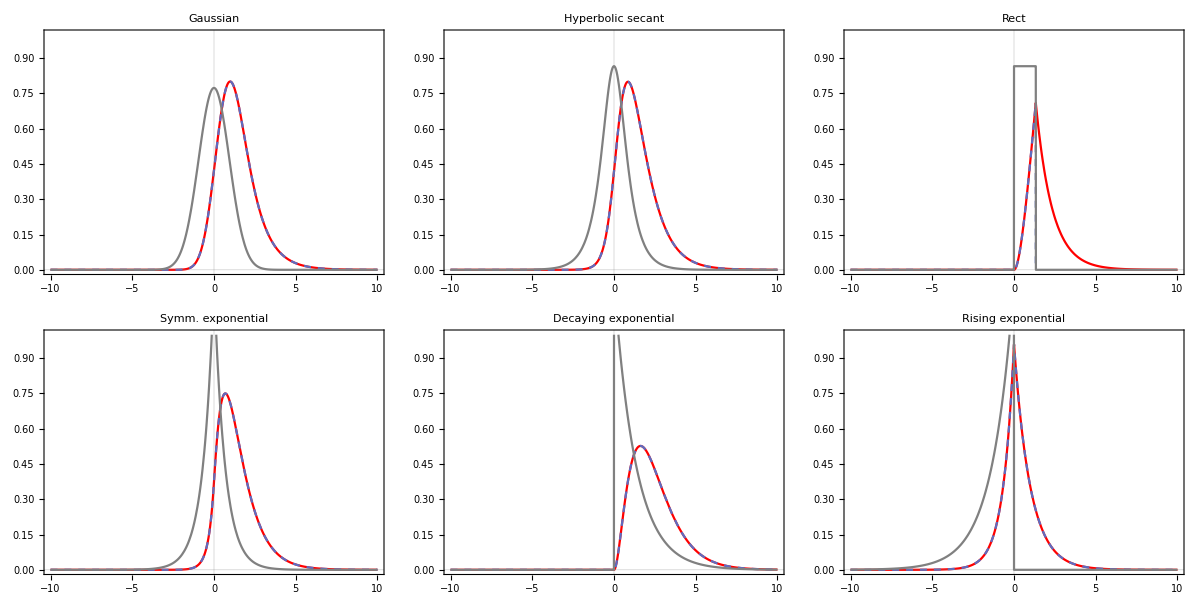

```mathematica
Grid[ArrayReshape[Table[Plot[{PeHLArr[[j]],PeLindbladArr[[j]],PulseArr[[j]]},{t,tmax-2(tmax),tmax},PlotLabel->PulseLegend[[j]],PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed,Gray}],{j,Range[Length[PulseArr]]}],{2,3}]]
```

### compare input-output theory and H.-L. for different coupling strengths - correct

#### define different coupling strengths and simulation parameters

```mathematica
Clear[Ω];
gaussian=(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];sech=√(Ω/2)Sech[Ω t];
rect=Piecewise[{{√(Ω/2),0<=t<=2/Ω},{0,t>2/Ω}}];
symm=√Ω Exp[-Ω Abs[t]];
decay=Piecewise[{{√Ω Exp[-Ω t/2],t>0}}];
rising=Piecewise[{{√Ω Exp[Ω t/2],t<0}}];
(*PulseArr={gaussian,sech,rect,symm,decay,rising};
PulseLegend={"Gaussian", "Hyperbolic secant", "Rect", "Symm. exponential", "Decaying exponential", "Rising exponential"};*)

pulse =gaussian;

Γ=1;
ΓpArr={0.1, 0.5,1}Γ;
Ω0=1.5Γ;

tmin=-100;
tmax=10;

Ω=Ω0;
```

#### Lindblad eq for different coupling strengths

```mathematica
(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[H,L,t,ρ,rho]
PeLindbladArr={};

PulseArr={};
For[i=1,i<Length[ΓpArr]+1,i++,
u=ΓpArr[[i]]pulse;
AppendTo[PulseArr,u];
uSquaredIntegral=Assuming[t∈Reals,Integrate[u^2/.t->τ,{τ,-∞,t}]];
gu=u/(√(1-uSquaredIntegral));

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I(√Γ)/2 gu(sm.dag[aa]-sp.aa);(*eq 8. our decay rate is already included in g*)

(*decay operator for atom excited state*)
L=√Γ sm + gu aa;(*decay and absorption*)

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeLindbladArr,Pe];
]
```

Time to run sim step 1: 0.0625

Time to run sim step 2: 0.046875

Time to run sim step 3: 0.0625

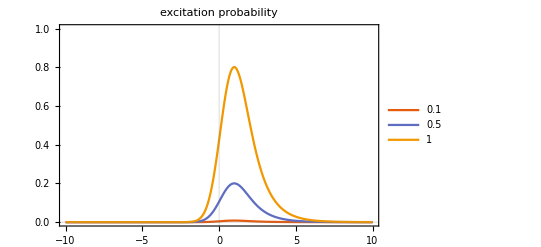

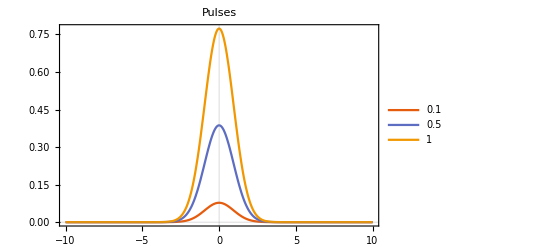

```mathematica
Plot[PeLindbladArr,{t,tmax-2tmax,tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"excitation probability",PlotRange->{{tmax-2tmax,tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2tmax,tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Heisenberg-Langevin eqs for different coupling strengths

```mathematica
Clear[s,M,b,t]
PeHLArr={};
PulseArr={};
For[i=1,i<Length[ΓpArr]+1,i++,
g=ΓpArr[[i]]pulse;
AppendTo[PulseArr,g];

M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeHLArr,Pe];
]
```

Time to run sim step 1: 0.015625

Time to run sim step 2: 0.

Time to run sim step 3: 0.

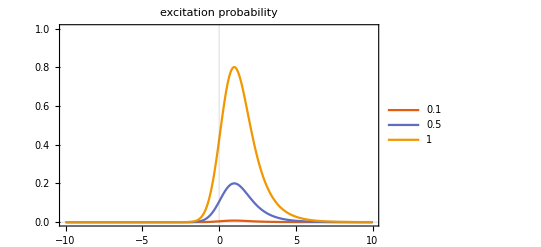

-Graphics-

```mathematica
Plot[PeHLArr,{t,tmax-2(tmax),tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax),tmax},PlotLegends->ΓpArr/Γ,PlotLabel->"Pulses",PlotRange->All,PlotTheme->"Scientific"]
```

#### Compare the solutions from the two methods

The plot below shows that the input-output theory Lindblad equation and Heisenberg-Langevin equations agree for all pulse shapes, except where t>2/Ω for the rectangular pulse, which is because Mathematica didn’t properly integrate it in the calculation of g(t).

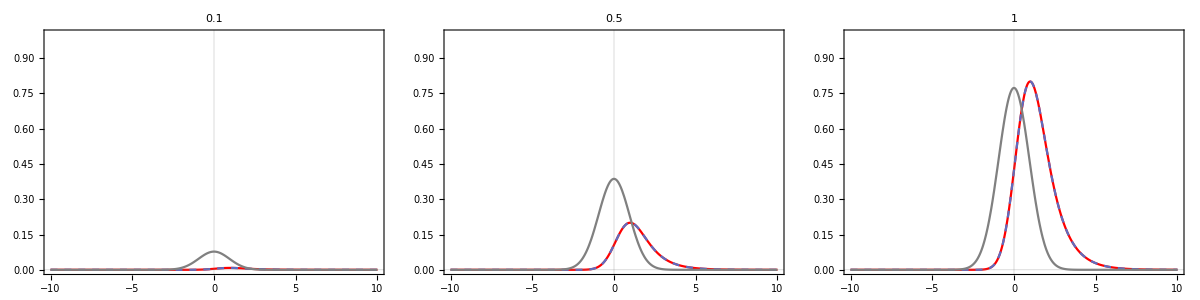

```mathematica
Grid[ArrayReshape[Table[Plot[{PeHLArr[[j]],PeLindbladArr[[j]],PulseArr[[j]]},{t,tmax-2(tmax),tmax},PlotLabel->ΓpArr[[j]],PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax),tmax},{0,1}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed,Gray}],{j,Range[Length[PulseArr]]}],{1,3}]]
```

## 4-level (classical fields) STIRAP

Get classical multi-level STIRAP working before making one of the fields a propagating single photon mode.

References: 
1. “Population transfer with delayed pulses in four-state systems” J. Oreg., ..., S. Rosenwaks.

Notes: STIRAP extended to use more than 3 states where the number of states is even, the single photon detunings must be finite or there is no dark state to follow.

## examples with Gaussian α,γ, constant β

```mathematica
(*seems like Ω=1.2Δ is about the right amount for these parameters*)
Δ1 = Δ2 = 10;
Ω0list={2,1.5,1.2,1,0.7,0.5}Δ1;
soln4arr={};
ψ0={1,0,0,0};
ρ0=Outer[Times,ψ0,ψ0];
L={};
(*start with atom in ground state*)
tmax=10;
tmin=-10;
For[i=1,i<Length[Ω0list]+1,i++,
w=2;
μ=0.8;
Ω0=Ω0list[[i]];
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=Ω0/2;
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];*)
{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H,L,tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
AppendTo[soln4arr,soln[[popIdcs[[4]],2]]]
]
```

Time to run sim step 1: 0.140625

Time to run sim step 2: 0.125

Time to run sim step 3: 0.109375

Time to run sim step 4: 0.140625

Time to run sim step 5: 0.109375

Time to run sim step 6: 0.125

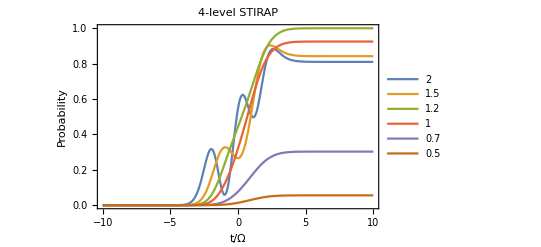

```mathematica
Plot[Evaluate[Table[soln4arr[[i]],{i,Range[Length[soln4arr]]}]],{t,tmin,tmax},PlotLegends->Ω0list/Δ1,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

```mathematica
soln4arr[[1]]
```

InterpolatingFunction[…][t]

Time to run sim: 0 mins

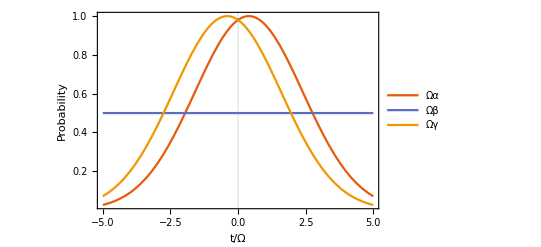

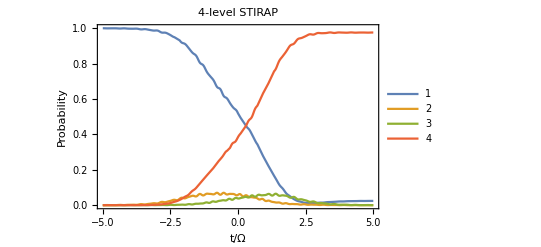

```mathematica
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotTheme->"Scientific"]
leg = {"1","2","3","4"};
plt=Plot[{Abs[soln[[1]]],Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

```mathematica
(*seems like Ω=1.5Δ is about the right amount*)
Ω0list={2,1.5,1,0.7,0.5}Δ1;
soln4arr={};
ψ0={1,0,0,0};
ρ0=Outer[Times,ψ0,ψ0];(*start with atom in ground state*)
tmax=5;
For[i=1,i<Length[Ω0list]+1,i++,
w=2;
μ=0.8;
Ω0=Ω0list[[i]];
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=Ω0/2;
Δ1 = Δ2 = 20;
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
AppendTo[soln4arr,soln[[4]]]
]
```

Time to run sim: 0 mins

Time to run sim: 0 mins

Time to run sim: 0 mins

«2 more identical outputs»

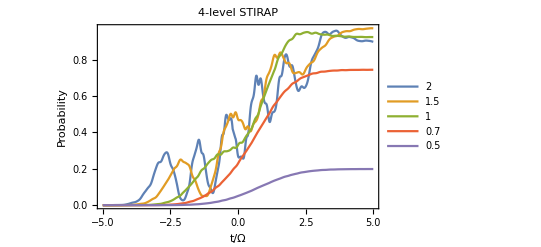

```mathematica
Plot[Evaluate[Table[Abs[soln4arr[[i]]]^2,{i,Range[Length[soln4arr]]}]],{t,-tmax,tmax},PlotLegends->Ω0list/Δ1,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## examples with Gaussian α,γ, decaying β

```mathematica
(*seems like Ω=1.2Δ is about the right amount for these parameters*)
Δ1 = Δ2 = 10;
Γ=0.01;(*decay rate for incoming field β*)
Ω0list={2,1.5,1.2,1,0.7,0.5}Δ1;
soln4arr={};
ψ0={1,0,0,0};
ρ0=Outer[Times,ψ0,ψ0];
L={};
(*start with atom in ground state*)
tmax=10;
tmin=-10;
tβ=-μ/2;
w=2;
μ=0.8;
For[i=1,i<Length[Ω0list]+1,i++,
Ω0=Ω0list[[i]];
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=(Ω0/2)Piecewise[{{Exp[-Γ (t-tβ)/2],(t-tβ)>0}}];
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];*)
{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H,L,tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
AppendTo[soln4arr,soln[[popIdcs[[4]],2]]]
]
```

Time to run sim step 1: 0.109375

Time to run sim step 2: 0.140625

Time to run sim step 3: 0.140625

Time to run sim step 4: 0.15625

Time to run sim step 5: 0.109375

Time to run sim step 6: 0.140625

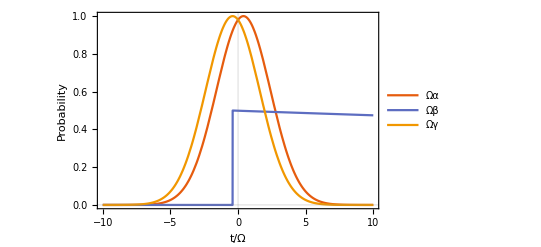

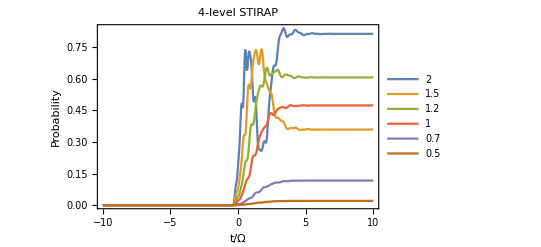

```mathematica
Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotTheme->"Scientific"]
Plot[Evaluate[Table[soln4arr[[i]],{i,Range[Length[soln4arr]]}]],{t,tmin,tmax},PlotLegends->Ω0list/Δ1,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

```mathematica
(*there is a benefit to turning on the β field earlier. this also seems to work the best when the decay envelope is ~ constant over the α,β pulse times.*)
Δ1 = Δ2 = 10;
Γ=0.01;(*decay rate for incoming field β*)
Ω0list={2,1.5,1.2,1,0.7,0.5}Δ1;
soln4arr={};
ψ0={1,0,0,0};
ρ0=Outer[Times,ψ0,ψ0];
L={};
(*start with atom in ground state*)
tmax=10;
tmin=-10;
tβ=-5μ;
w=2;
μ=0.8;
For[i=1,i<Length[Ω0list]+1,i++,
Ω0=Ω0list[[i]];
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=(Ω0/2)Piecewise[{{Exp[-Γ (t-tβ)/2],(t-tβ)>0}}];
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];*)
{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H,L,tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
AppendTo[soln4arr,soln[[popIdcs[[4]],2]]]
]
```

Time to run sim step 1: 0.1875

Time to run sim step 2: 0.140625

Time to run sim step 3: 0.140625

Time to run sim step 4: 0.15625

Time to run sim step 5: 0.140625

Time to run sim step 6: 0.125

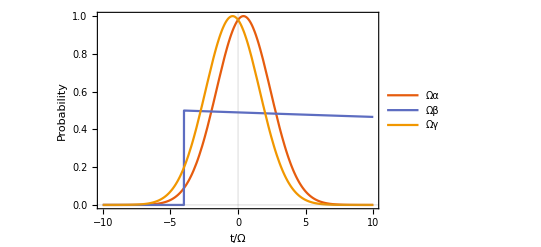

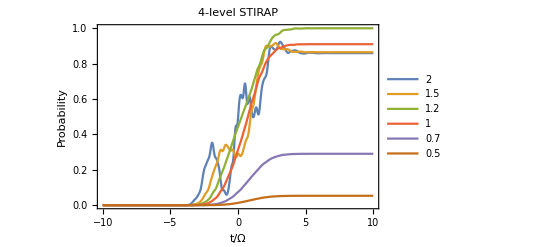

```mathematica
Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotTheme->"Scientific"]
Plot[Evaluate[Table[soln4arr[[i]],{i,Range[Length[soln4arr]]}]],{t,tmin,tmax},PlotLegends->Ω0list/Δ1,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## multi-level STIRAP w/ single photon

The diagram above illustrates the goal of absorbing a telecom single photon Fock state, with the assistance of two coupling fields. The 780 probe should not be resonant, however, as we want to do a three-field four level STIRAP process. See, e.g., “Stimulated Raman adiabatic passage in physics, chemistry, and beyond” section IV.

Some questions-- 
* should I trace over the field to get eqs for only the atom? this ought to make it easier to make a correspondence with classical chained STIRAP eqs, but isn’t strictly necesarry.
 * resonant or off-resonant STIRAP? either can be done, but there may be physics reasons for doing one vs the other, such as being able to tune the receiver atom to be insensitive to the exact frequency of the photon it is receiving (which depends on level shifts on the atom that emitted it).